```mathematica
(*Quit[]*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

```mathematica
(*Ebert, Faustov, Galkin, arXiv:1007.1369 [hep-ph]*)
```

## Init

```mathematica
<<MyPackages`ChDim`
```

```mathematica
<<MyPackages`HistV2`
```

```mathematica
SetOptions[ChDim, Dimensions->{
GF->-2,
a1->0, beta->0, Vbc->0, Vuq->0,
mu->0,a->0, b->0,
rhoL[_]->0, rhoT[_]->0,
fPlus[_]->0, fMinus[_]->0,
hA[_]->0, hV1[_]->0, hV2[_]->0, hV3[_]->0,
tV[_]->0, tA1[_]->0, tA2[_]->0, tA3[_]->0,
fP->1, mP->1, fV->1, mV->1,
p1->1, p2->1,q->1, MBc->1, Mcc->1,
q2->2}];
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
<<"./mdat/ebert_ff.mdat";
```

## Intro

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
(* 1P masses from PDG *)
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
(* 2P masses are chosen to fit Ebert's distributions *)
getMcc[out_, "2P"]:=Switch[out,"chi_c0", 3862MeV,"chi_c1", 3.9214,"chi_c2",3.967735]
```

```mathematica
GeV=1.; MeV=10^-3 GeV;
```

```mathematica
$MBc = 6274.47MeV;
$mPi = 0.140GeV;
$a1 = 1.14;
Clear[Ngamma];
Ngamma[out_, outL_, type_:"1P"]:=Module[{
$Mcc=getMcc[out, type],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2],
fffit = Switch[type,"1P",ffFitRule,"2P", ffFitRule$2P]
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->208MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->$a1
}//.{MBc -> $MBc, mPi->$mPi, mV->775MeV, Mcc->$Mcc, q2->$q2}/.fffit]
Ngamma[out_, "enu",type_:"1P"]:=Ngamma[out,"W", type]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}
```

```mathematica
Clear[q2Max];
q2Max[out_,type_:"1P"]:=($MBc-getMcc[out,type])^2;
```

## Two-Body Decays

```mathematica
Clear[$gamma];
$gamma::usage="$gamma[out, outL, type] is the width of Bc -> out outL decay from tables II, VI (in 10^-15GeV)";
$gamma[out_,outL_]:=$gamma[out,outL,"1P"];
(* Table VI *)
$gamma["chi_c0","P","1P"] = 0.23($a1)^2;
$gamma["chi_c0","V","1P"] = 0.64($a1)^2;
$gamma["chi_c1","P","1P"] = 0.22($a1)^2;
$gamma["chi_c1","V","1P"] = 0.16($a1)^2;
$gamma["chi_c2","P","1P"] = 0.41($a1)^2;
$gamma["chi_c2","V","1P"] = 1.18($a1)^2;
(**)
$gamma["chi_c0","P","2P"] = 0.023($a1)^2;
$gamma["chi_c0","V","2P"] = 0.080($a1)^2;
$gamma["chi_c1","P","2P"] = 0.011($a1)^2;
$gamma["chi_c1","V","2P"] = 0.016($a1)^2;
$gamma["chi_c2","P","2P"] = 8.5*10^-7($a1)^2;
$gamma["chi_c2","V","2P"] = 0.0022($a1)^2;
```

```mathematica
outL="P"; type="1P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(1P) P:	 this/Ebert=0.987324

Bc ->chi_c1(1P) P:	 this/Ebert=0.0582581

Bc ->chi_c2(1P) P:	 this/Ebert=0.958299

```mathematica
outL="V"; type="1P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(1P) V:	 this/Ebert=0.703591

Bc ->chi_c1(1P) V:	 this/Ebert=0.865832

Bc ->chi_c2(1P) V:	 this/Ebert=0.694878

```mathematica
outL="P"; type="2P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(2P) P:	 this/Ebert=1.0626

Bc ->chi_c1(2P) P:	 this/Ebert=0.378969

Bc ->chi_c2(2P) P:	 this/Ebert=39.3025

```mathematica
outL="V"; type="2P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(2P) V:	 this/Ebert=0.784713

Bc ->chi_c1(2P) V:	 this/Ebert=0.840521

Bc ->chi_c2(2P) V:	 this/Ebert=1.16257

## Semileptonic decays

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

```mathematica
distEE["chi_c0"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic0_1P.json"], 1]["data"];
distEE["chi_c1"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic1_1P.json"], 1]["data"];
distEE["chi_c2"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic2_1P.json"], 1]["data"];
```

```mathematica
distEE["chi_c0","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic0_2P.json"], 1]["data"];
distEE["chi_c1","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic1_2P.json"], 1]["data"];
distEE["chi_c2","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic2_2P.json"], 1]["data"];
```

```mathematica
Clear[$br];
$br::usage="$br[out, outL] --- numerical values of the width (in 10^15), see  Table II";
$br["chi_c0", "enu"]=1.27;
$br["chi_c1", "enu"]=1.18;
$br["chi_c2","enu"]=2.27;
```

```mathematica
Clear[genENuPlot];
genENuPlot::usage = "genENuPlot[out]";
genENuPlot[out_]:=Module[{},
root=ReadList["../c++/results/B_c+_"<>out<>"_enu_ff1/m2_0m1.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
Print["Br[this]/Br[Ebert]=",10^15 NIntegrate[Ngamma[out,"enu"],{q2,0,q2Max[out]}]/$br[out, "enu"]];
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"enu"], {q2, 0.2,8}],
ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
];
```

```mathematica
genENuPlot["chi_c0"]
```

Br[this]/Br[Ebert]=1.23488

-Graphics-

```mathematica
genENuPlot["chi_c1"]
```

Br[this]/Br[Ebert]=1.19999

-Graphics-

```mathematica
genENuPlot["chi_c2"]
```

Br[this]/Br[Ebert]=1.20688

-Graphics-

### nπ decays

```mathematica
Clear[readROOT];
Options[readROOT]={Norm->False, Color->Red};
readROOT[fileName_,OptionsPattern[]]:=Module[{root},
root = ReadList[fileName,{Number,Number,Number}];
If[Head[root]=!=List,
Print["File not found",  fileName];
Abort[];
];
root = HST2D[{#⟦1⟧,#⟦2⟧±#⟦3⟧}&/@root, PlotStyle->OptionValue[Color]];
If[OptionValue[Norm]=!=False,
root *= OptionValue[Norm]/IntegralHST[root];
];
root
]
```

```mathematica
<<"./mdat/rhoT.mdat";
```

```mathematica
<<MyPackages`HistV2`
```

```mathematica
Clear[brNPI];
brNPI::usage="brNPI[out, n]";
```

```mathematica
Clear[genNPiPlot];
genNPiPlot::usage="genNPiPlot[out, mPi]";
genNPiPlot[out_, nPi_]:=Module[{},
mode = ToString[nPi]<>"pi";react= "Bc→"<>out<>" "<>mode;
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->ConstNπ[nPi]*FqNπ[nPi]},{q2, (nPi*$mPi)^2,q2Max[out]}];
brNPI[out, nPi]=br;
Print["Br["<>react<>"]=",br," %"];
root = readROOT["../c++/results/B_c+_"<>out<>"_"<>mode<>"_ff1/m2_0m1.txt",Norm->br];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->ConstNπ[nPi]*FqNπ[nPi]},{q2, (nPi*$mPi)^2,q2Max[out]}, PlotRange->All]
,PlotRange->All, PlotLabel->react]
]
```

Br[Bc→chi_c0 2pi]=0.0597652 %

Br[Bc→chi_c1 2pi]=0.0185221 %

Br[Bc→chi_c2 2pi]=0.108223 %

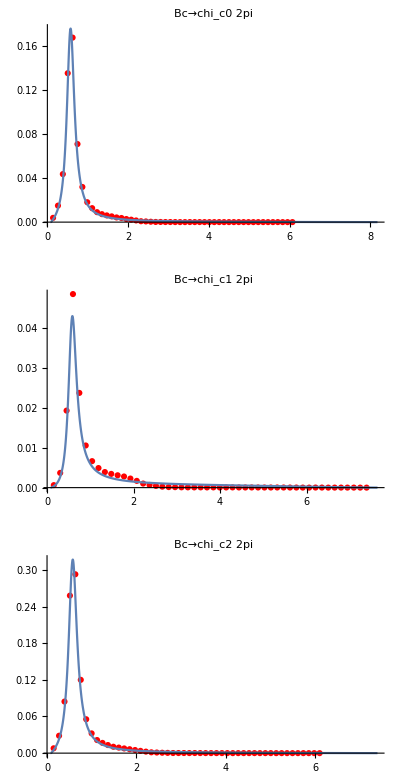

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 2],{out, chiList}]}//Transpose]
```

Br[Bc→chi_c0 3pi]=0.0371442 %

Br[Bc→chi_c1 3pi]=0.0229855 %

Br[Bc→chi_c2 3pi]=0.068821 %

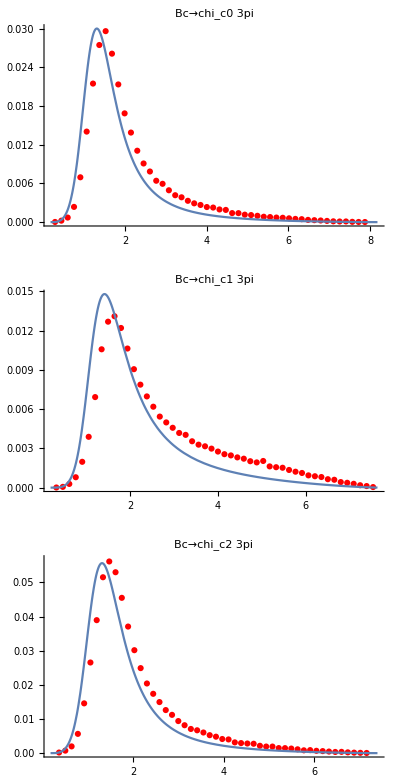

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 3],{out, chiList}]}//Transpose]
```

Br[Bc→chi_c0 5pi]=0.00378203 %

Br[Bc→chi_c1 5pi]=0.00462799 %

Br[Bc→chi_c2 5pi]=0.00656311 %

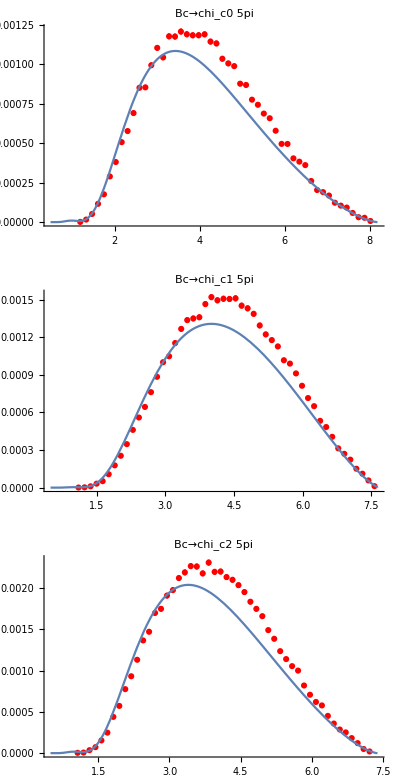

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 5],{out, chiList}]}//Transpose]
```